```mathematica
Cfunc[y_]=9*Integrate[(x^4*E^x)/(E^x-1)^2,{x,0,y}]
```

ConditionalExpression[9 (-(4 π^4)/15+1/(-1+ⅇ^y)(-ⅇ^y y^4-4 y^3 Log[1-ⅇ^y]+4 ⅇ^y y^3 Log[1-ⅇ^y]+12 (-1+ⅇ^y) y^2 PolyLog[2,ⅇ^y]-24 (-1+ⅇ^y) y PolyLog[3,ⅇ^y]-24 PolyLog[4,ⅇ^y]+24 ⅇ^y PolyLog[4,ⅇ^y])),ⅇ^y≤1]

```mathematica
a = 9*Integrate[(x^4*E^x)/(E^x-1)^2,{x,0,∞}]
```

(12 π^4)/5

```mathematica
CLow[x_]=a*x^3
```

(12 π^4 x^3)/5

```mathematica
Series[(x^4*E^x)/(E^x-1)^2,{x,0,1}]
```

O[x]^2

The integrand at the limit T>>Θ is x^2, so evaluating the integral gives (Θ/T)^3. Therefore C=3Nk_b

```mathematica
CHigh[x_]=3
```

3

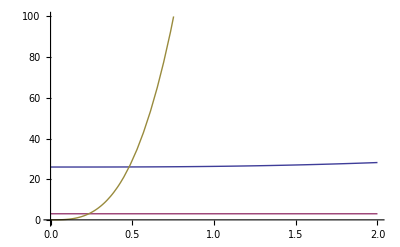

```mathematica
Plot[{-x^4-x^4/(-1+E^x)+4 x^3 Log[1-E^x]+12 x^2 PolyLog[2,E^x]-24 x PolyLog[3,E^x]+24 PolyLog[4,E^x], CHigh[x], CLow[x]}, {x,0,2}, PlotRange->{{0,2},{-1,100}}]
```